# Part B: Finite Difference Calculations of Scattering Wave Functions

B1:
a)

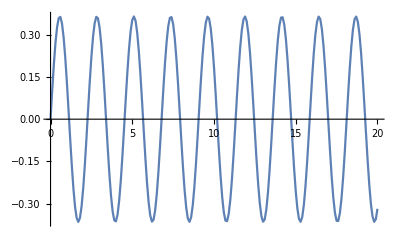

```mathematica
Clear[HeConst,energy,uRawData]
xmin = 0;
xmax = 20;
u[0] = 0;
u[1] = 0.1;
h=0.1;
subs={Heconst-> 0.523, energy-> 4};
nSteps:=Round[(xmax-xmin)/h]
Do[
u[n+1]=((-h^2*energy/Heconst+2) u[n]-u[n-1])/.subs,
{n,1,nSteps}]
uRawData:= Table[{u[n]},{n,0,nSteps}];
uMax := Max[uRawData];
uData := Table[{xmin+n h, u[n]},{n,0,nSteps}];
uNumPlot=ListPlot[uData,Joined->True];
Show[uNumPlot]
```

b)

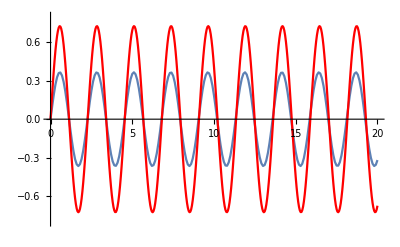

```mathematica
h= 0.05;
Do[
u[n+1]=((-h^2*energy/Heconst+2) u[n]-u[n-1])/.subs,
{n,1,nSteps}]
half = ListPlot[uData, Joined -> True,PlotStyle-> Red];
Show[uNumPlot,half, PlotRange -> {-.8,.8}]
```

In this case the amplitude depends on the step size because the wavefunction is not normalized, This could be done by finding the normalization constant.

c)
Using Schrodinger’s time independent equation we find k by plugging in the analytical solution into the equation and solve for k.

```mathematica
Psi[x_] := A*Sin[k*x] + B*Cos[k*x]
Print["energy  = "-ℏ^2/(2m) *Simplify[D[D[Psi[x],x],x]/ℏ[x]] /Psi[x]]
```

energy  = +(k^2 ℏ^2)/(2 m ℏ[x])

Therefore through algebra we solve for k and get k==(√(2mE))/(h̄)

d)
Using Ψ(0)==Csin(θ), we can approximate the wavenumber and wavelenght.

{A→0.73,k→2.78,θ→0}

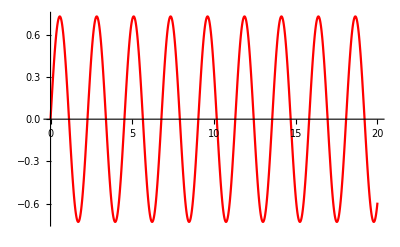

Setting TraditionalForm`Ψ(0) == 0 ,  θ==sin^-1((Ψ(0))/C)==0
The amplitude is {0.730}, so C = 0.730, and the first peak occurs at about x=0.55, and the next peak occurs at about 2.83, indicating a wavelength of 2.28 A. Therefore we obtain a wavenumber of k = 2.78. The Plot using these parameters is displayed below.

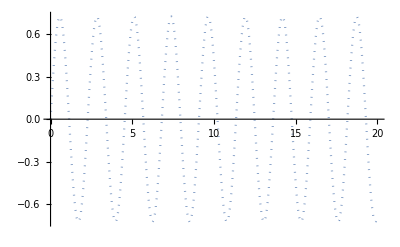

Together these plots are superimposed and provide an optimal fit as shown below

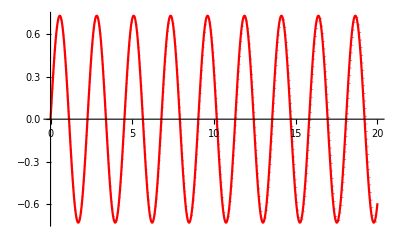

```mathematica
(*approximating the wavefunction *)
subs = {A-> 0.730, k->2.78, θ-> 0}
Uapprox[x_] :=A*Sin[k*x+θ]/.subs;
Uapr = Plot[Uapprox[x],{x,0,20},PlotStyle-> Red]
Print["Setting TraditionalForm`Ψ(0) == 0 ,  θ==sin^-1((Ψ(0))/C)==0
The amplitude is {0.730}, so C = 0.730, and the first peak occurs at about x=0.55, and the next peak occurs at about 2.83, indicating a wavelength of 2.28 A. Therefore we obtain a wavenumber of k = 2.78. The Plot using these parameters is displayed below."]
halff = ListPlot[uData, Joined -> True,PlotStyle-> Dotted]
Print["Together these plots are superimposed and provide an optimal fit as shown below"]
Show[halff,Uapr]
```

B2:
a)

10000

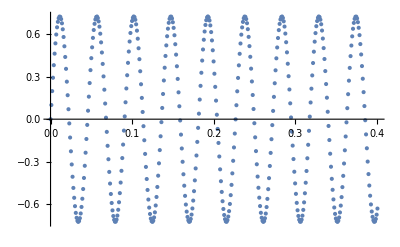

```mathematica
V[x_]=0;
f[x_]=-(2m/ℏ^2)(Energy-V[x]);
Subs={ℏ->1,m->1,Energy->20};
xMax=10;
h=0.001;
nSteps=Round[xMax/h]
PSI[0]=0;
PSI[1]=2.5;
Do[
PSI[n+1]=(2+h^2 f[h n])PSI[n]-PSI[n-1]/.Subs;
,{n,1,nSteps}]
norm=Sum[PSI[n]^2h,{n,0,nSteps}];
URawData=Table[PSI[n]/norm,{n,0,nSteps }];uMax=Max[uRawData];
UData=Table[{h n,PSI[n]/norm},{n,0,nSteps }];
UNumPlot=ListPlot[uData]
```